```mathematica
付録A   User Manual of Mathematica

Q A.1.1
```

```mathematica
(1)
```

```mathematica
Solve[x^4 + 2 x^2 - 4x + 8 == 0,x]
```

{{x→1-ⅈ},{x→1+ⅈ},{x→-1-ⅈ √3},{x→-1+ⅈ √3}}

```mathematica
(2)
```

```mathematica
Solve[{x y + x ; y == -3 , yz + y + z == -7,zx + z +x == 11},{x,y,z}]
```

```mathematica
{{x->15+yz-zx,y->-3,z->-4-yz}}
```

```mathematica
QA.2.1
```

```mathematica
Clear[x]
RSolve[{x[0]==1,x[n]==x[n-1]+n},x[n],n]
```

{{x[n]→1/2 (2+n+n^2)}}

```mathematica
Clear[x]
FunctionExpand[RSolve[{x[1]==0,x[2]==1,x[n+2] == x[n+1] + x[n]},x[n],n]]//FullSimplify
```

{{x[n]→1/10 (-(-5+√5) (1/2 (1+√5))^n+(1/2 (-1+√5))^n (5+√5) Cos[n π])}}

```mathematica
Clear[x]
```

```mathematica
QA.3微分積分
```

```mathematica
D[Sin[x]Cos[x],{x,2}]//FullSimplify
```

-4 Cos[x] Sin[x]

```mathematica
f[x_,y_] := 1/2 * Log[x^2 + y^2];
D[f[x,y],{x,2}] + D[f[x,y],{y,2}]
```

1/2 (-(4 x^2)/((x^2+y^2)^2)+2/(x^2+y^2))+1/2 (-(4 y^2)/((x^2+y^2)^2)+2/(x^2+y^2))

```mathematica
QA.3.3
```

```mathematica
Integrate[1/(√(1 + x^2)),x]
```

ArcSinh[x]

```mathematica
Integrate[1/(1 + x^2),{x,-1,1}]
```

π/2

```mathematica
広義積分
```

```mathematica
Integrate[Log[Sin[x]],{x,0,Pi/2}]//FullSimplify
```

-1/2 π Log[2]

```mathematica
Integrate[Sin[x]/(√x),{x,0,Infinity}]
```

√(π/2)

```mathematica
4* Integrate[1/(√(x^2+y^2)),{x,0,1},{y,0,√(1-x^2)}]//FullSimplify
```

2 π

```mathematica
A.4行列
```

```mathematica
Q A.4.1
```

```mathematica
a={{1,2},{3,4}};
b ={{5,6},{7,8}};
MatrixPower[a,2]+MatrixPower[b,2]+a b + 3 a + 4 a //MatrixForm
```

(86 | 114
148 | 188)

```mathematica
Clear[a,b]
```

```mathematica
Q A.4.2
```

```mathematica
a={{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}};
Det[a]
Tr[a]
Transpose[a]//MatrixForm
Inverse[a]
```

0

34

(1 | 5 | 9 | 13
2 | 6 | 10 | 14
3 | 7 | 11 | 15
4 | 8 | 12 | 16)

Inverse::sing: Matrix {{1, 2, 3, 4}, {5, 6, 7, 8}, {9, 10, 11, 12}, {13, 14, 15, 16}} is singular.

Inverse[{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}]

```mathematica
QA.4.3
```

```mathematica
Clear[a]
```

```mathematica
a={{1,0,2},{0,2,0},{2,0,1}}
```

{{1,0,2},{0,2,0},{2,0,1}}

```mathematica
Eigenvalues[a]
Eigenvectors[a]
Eigensystem[a]
```

{3,2,-1}

{{1,0,1},{0,1,0},{-1,0,1}}

{{3,2,-1},{{1,0,1},{0,1,0},{-1,0,1}}}

```mathematica
グラフ
QA.5.1
```

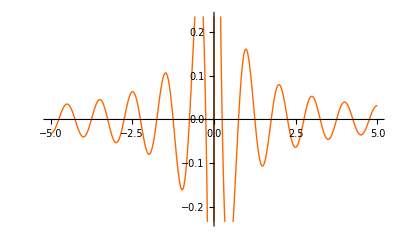

```mathematica
Plot[Cos[2 Pi x]/(2 Pi x),{x,-5,5},PlotStyle->{RGBColor[1,0.4,0]}]
```

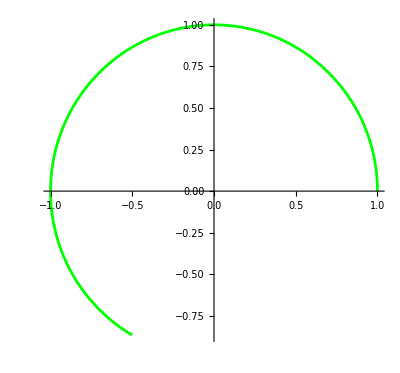

```mathematica
f1 = {Cos[t],Sin[t]};
g1= ParametricPlot[f1,{t,0,4 Pi / 3},AspectRatio->Automatic,PlotStyle->{Thickness[0.005],RGBColor[0,1,0]},PlotRange->All]
```

```mathematica
Q A.5.2
```

```mathematica
Clear[f,x,y];
x= t Cos[1/t];
y = t Sin[1/t];
f = {x,y};
```

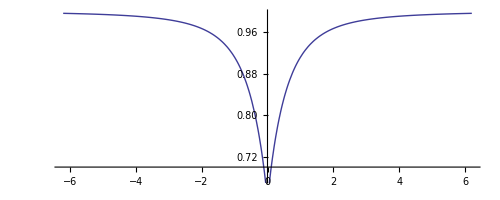

```mathematica
ParametricPlot[{t Cos[1/t],t Sin[1/t]},{t,-2*Pi,2*Pi}]
```

```mathematica
gf = Plot3D[Sin[2 Pi √(x^2 + y^2)],{x,-1,1},{y,-1,11}]
```

-Graphics3D-

```mathematica
Show[gf,ViewPoint->{0,2,0}]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[2 Pi √(x^2 + y^2)],{x,-100,100},{y,-100,100}]
```

-Graphics-

```mathematica
A.6微分方程式
```

```mathematica
Clear[x,y]
DSolve[x y ''[x] + (1 - 2 x)y' [x]+ (x - 1)y[x] == 4 x Exp[x],y[x],x]
```

{{y[x]→ⅇ^x x^2+ⅇ^x C[1]+ⅇ^x C[2] Log[x]}}

```mathematica
DSolve[{x''[t]== k - x [t]/10, x[0] == 0,x'[0] == 1},x[t],t ]
```

{{x[t]→10 k-10 k Cos[t/(√10)]+√10 Sin[t/(√10)]}}

```mathematica
DSolve[{x'[t]==x[t]+y[t],y'[t]==-x[t],x[0]==1/10000,y[0]==1},{x[t],y[t]},t]//FullSimplify
```

{{x[t]→(ⅇ^(t/2) (Cos[(√3 t)/2]+6667 √3 Sin[(√3 t)/2]))/10000,y[t]→(ⅇ^(t/2) (5000 Cos[(√3 t)/2]-1667 √3 Sin[(√3 t)/2]))/5000}}